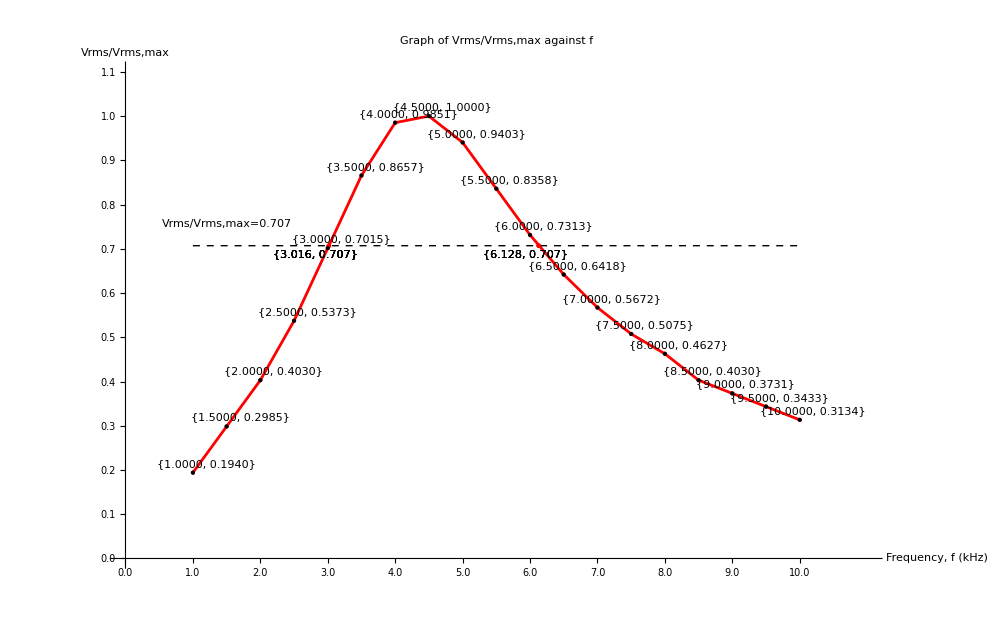

```mathematica
data={{1.0,0.1940},{1.5,0.2985},{2.0,0.4030},{2.5,0.5373},{3.0,0.7015},{3.5,0.8657},{4.0,0.9851},{4.5,1.0000},{5.0,0.9403},{5.5,0.8358},{6.0,0.7313},{6.5,0.6418},{7.0,0.5672},{7.5,0.5075},{8.0,0.4627},{8.5,0.4030},{9.0,0.3731},{9.5,0.3433},{10.0,0.3134}};

intersectionPoints={x,0.707}/. Table[FindRoot[Interpolation[data][x]==0.707,{x,xi}],{xi,1,10,1}];

ListLinePlot[data,PlotStyle->Red,Mesh->All,MeshStyle->PointSize[Medium],AxesLabel->{"Frequency, f (kHz)","Vrms/Vrms,max"},PlotLabel->"Graph of Vrms/Vrms,max against f",Epilog->{Dashed,Line[{{1,0.707},{10,0.707}}],Red,PointSize[Medium],Point[intersectionPoints],Text[Style[ToString@NumberForm[#,{4,3}],Black],#-{0.2,0.02}]&/@intersectionPoints,Black,PointSize[Medium],Point[data],Text[Style[ToString@NumberForm[#,{4,4}],Black],#+{0.2,0.02}]&/@data,Text["Vrms/Vrms,max=0.707",{1.5,0.707+0.05}]},PlotRange->{{0,11.0},{0,1.1}},
Ticks->{{#,NumberForm[#,{3,1}]}&/@Range[0,10.5,0.5],{#,NumberForm[#,{3,1}]}&/@Range[0,1.1,0.1]}
]
```